# COMPUTER LESSON 3

## Theory

### SETS

```mathematica
a = {0, 2, 4, 6, 8, 10}
```

{0,2,4,6,8,10}

```mathematica
a1 = Table[i, {i, 0, 10, 2}]
```

{0,2,4,6,8,10}

```mathematica
b = Table[i,{i,0,6}]
```

{0,1,2,3,4,5,6}

```mathematica
c=Table[i,{i,4,10}]
```

{4,5,6,7,8,9,10}

### Union of sets

```mathematica
u=Union[a,b,c]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Length[u]
```

11

### Intersection

```mathematica
i = Intersection[a,b,c]
```

{4,6}

```mathematica
u[[8]](*the element 8 of the union list*)
```

7

### Complement [A,B]=A-B

```mathematica
Intersection[Complement[a,b],Complement[a,c],Complement[b,c]]
```

{}

```mathematica
Union[Complement[a,b],Complement[a,c]]
```

{0,2,8,10}

```mathematica
Complement[a,Intersection[b,c]]
```

{0,2,8,10}

### Subsets(*all the subsets of a set*)

```mathematica
s=Subsets[a](*power sets of a*)
```

{{},{0},{2},{4},{6},{8},{10},{0,2},{0,4},{0,6},{0,8},{0,10},{2,4},{2,6},{2,8},{2,10},{4,6},{4,8},{4,10},{6,8},{6,10},{8,10},{0,2,4},{0,2,6},{0,2,8},{0,2,10},{0,4,6},{0,4,8},{0,4,10},{0,6,8},{0,6,10},{0,8,10},{2,4,6},{2,4,8},{2,4,10},{2,6,8},{2,6,10},{2,8,10},{4,6,8},{4,6,10},{4,8,10},{6,8,10},{0,2,4,6},{0,2,4,8},{0,2,4,10},{0,2,6,8},{0,2,6,10},{0,2,8,10},{0,4,6,8},{0,4,6,10},{0,4,8,10},{0,6,8,10},{2,4,6,8},{2,4,6,10},{2,4,8,10},{2,6,8,10},{4,6,8,10},{0,2,4,6,8},{0,2,4,6,10},{0,2,4,8,10},{0,2,6,8,10},{0,4,6,8,10},{2,4,6,8,10},{0,2,4,6,8,10}}

```mathematica
Length[s]
```

64

```mathematica
2^6
```

64

### Divisibility

gcd is the greatest common divisor

```mathematica
GCD[18,12]
```

6

lcm is least common multiple

```mathematica
LCM[18,12]
```

36

```mathematica
GCD[18,12]*LCM[18,12](*same as 18*12*)
```

216

```mathematica
18*12
```

216

```mathematica
PrimeQ[101](*in order to know if the number is prime*)
```

True

```mathematica
l=Table[Prime[i],{i,1,100}](*the first 100 prime numbers*)
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
l2=Table[i,{i,1,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
l3=Intersection[l,l2](*to know the prime numbers under 100*)
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Length[l3]
```

25

```mathematica
CoprimeQ[25,9](*if they don't have any divisor in common*)
```

True

```mathematica
NextPrime[23](*the following prime number*)
```

29

```mathematica
NextPrime[24]
```

29

```mathematica
FactorInteger[18](*2^1*.083^2*)
```

{{2,1},{3,2}}

```mathematica
Divisors[18](*numbers that can divide the number*)
```

{1,2,3,6,9,18}

### Combinatorics

Combinations

```mathematica
Binomial[3,2](*3 choose 2*)
```

3

Permutations

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
3!
```

6

Variations: Binomial[m, n]*n!

```mathematica
Binomial[5,2]*2!
```

20

## Functions

```mathematica
Clear["Global`*"]
```

### ex1

```mathematica
a=Table[i,{i,0,10,2}]
```

{0,2,4,6,8,10}

```mathematica
b=Table[i,{i,0,6}]
```

{0,1,2,3,4,5,6}

```mathematica
c=Table[i,{i,4,10}]
```

{4,5,6,7,8,9,10}

```mathematica
Union[a,b,c]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Intersection[a,b,c]
```

{4,6}

```mathematica
Intersection[{Complement[a,b]},{Complement[a,c]},{Complement[b,c]}]
```

{}

### ex2

```mathematica
e=Table[i,{i,0,200,2}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200}

```mathematica
a1=Table[i,{i,0,200,5}]
```

{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200}

```mathematica
a=Intersection[e,a1]
```

{0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200}

```mathematica
b1=Table[i,{i,0,150}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150}

```mathematica
b=Intersection[e,b1]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150}

```mathematica
Intersection[a,b]
```

{0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150}

```mathematica
Complement[e,a]
```

{2,4,6,8,12,14,16,18,22,24,26,28,32,34,36,38,42,44,46,48,52,54,56,58,62,64,66,68,72,74,76,78,82,84,86,88,92,94,96,98,102,104,106,108,112,114,116,118,122,124,126,128,132,134,136,138,142,144,146,148,152,154,156,158,162,164,166,168,172,174,176,178,182,184,186,188,192,194,196,198}

```mathematica
Complement[e,b]
```

{152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200}

```mathematica
Union[a,b]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,160,170,180,190,200}

```mathematica
Length[a]
```

21

### Ex3

```mathematica
f[x_]=-3x+4
```

4-3 x

```mathematica
f[0]
```

4

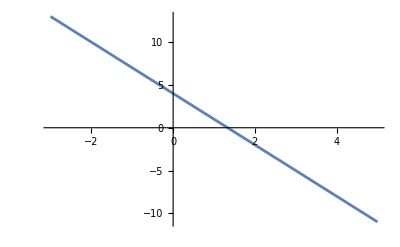

```mathematica
Plot[f[x],{x,-3,5}]
```

```mathematica
Solve[f[x1]==f[x2],{x1,x2}](*==for equation, = for assign values*)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→x1}}

```mathematica
Solve[x^2-5x+6==0,x]
```

{{x→2},{x→3}}

```mathematica
Solve[{x+y==5,x-y==3},{x,y}]
```

{{x→4,y→1}}

```mathematica
Reduce[{x+a*y==5,x-a*y==3},{x,y}](*a is a parameter*)
```

x==4&&a≠0&&y==1/a

```mathematica
Reduce[x+a*y==5&&x-a*y==3,{x,y}](*bracets can be replaced by &&*)
```

x==4&&a≠0&&y==1/a

### ex4

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=x^2+1
```

1+x^2

```mathematica
g[x_]=x+2
```

2+x

```mathematica
g[f[x]]
```

3+x^2

```mathematica
f[g[x]]
```

1+(2+x)^2

```mathematica
f[g[x]]//Expand (*same solution but expanded*)
```

5+4 x+x^2

### ex5

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=a*x
```

a x

```mathematica
g[x_]=c*x+d
```

d+c x

```mathematica
f[g[x]]//Expand
```

a d+a c x

```mathematica
g[f[x]]//Expand
```

d+a c x

```mathematica
Reduce[f[g[x]]==g[f[x]],x]
```

a==1||d==0

a = 1 && c,d ∈ R
d = 0 && a,c ∈ R
paletas//otros//composicion tipografia basica

### ex6

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{357/101 x+47/111,x<=0},{2x-1,x>0}}](*for the divission ctr+shift+/*)
```

Piecewise[{{47/111+(357 x)/101, x≤0}, {-1+2 x, x>0}, {0, True}}]

```mathematica
f[3]
```

5

```mathematica
f[1/2]
```

0

```mathematica
f[-1]
```

-34880/11211

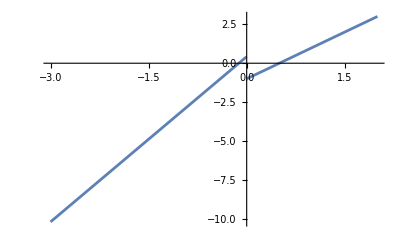

```mathematica
Plot[f[x],{x,-3,2}]
```

```mathematica
??Plot
```

### ex7

```mathematica
FactorInteger[10848]
```

{{2,5},{3,1},{113,1}}

```mathematica
FactorInteger[137562]
```

{{2,1},{3,1},{101,1},{227,1}}

### ex8

```mathematica
Solve[(Binomial[n,3]*3!)==(Binomial[n,4]*4!),{n}]
```

{{n→0},{n→1},{n→2},{n→4}}

So as n can’t be less than  4, the only possible anwser is n=4.

### ex9

```mathematica
Binomial[100,5]
```

75287520

### ex10

```mathematica
GCD[177650,101898]
```

34

```mathematica
LCM[177650,101898]
```

532417050

```mathematica
GCD[177650,101898]*LCM[177650,101898]
```

18102179700

```mathematica
177650*101898
```

18102179700

## Exam

### 2023MT

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{-x-2,x<=-2},{x^2-4,-2<x<0},{-x^3-4,x>=0}}]
```

Piecewise[{{-2-x, x≤-2}, {-4+x^2, -2<x<0}, {-4-x^3, x≥0}, {0, True}}]

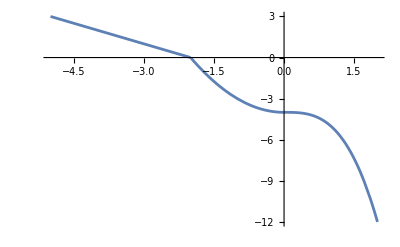

```mathematica
Plot[f[x],{x,-5,2}]
```

```mathematica
g[x_]= Piecewise[{{-2^x,x<=0},{-Cos(x),0<x<π/2},{x-π/2,x>=π/2}}]
```

Piecewise[{{-2^x, x≤0}, {-Cos x, 0<x<π/2}, {-π/2+x, x≥π/2}, {0, True}}]

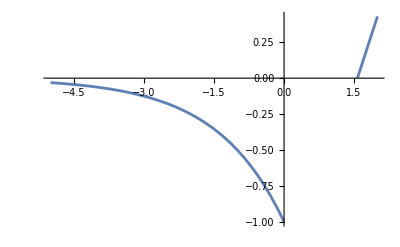

```mathematica
Plot[g[x],{x,-5,2}]
```